0.003

0.003

0

0.5

ArcTan[(4.×10^-6)/(z √(8.×10^-6+z^2))]

0.0005

0.0005

-0.5 (-1.42996+3 ArcTan[(4.×10^-6)/(√(8.×10^-6+(-0.0002-z)^2) (-0.0002-z))]+ArcTan[(4.×10^-6)/(z √(8.×10^-6+z^2))]+3 ArcTan[(4.×10^-6)/((0.0002+z) √(8.×10^-6+(0.0002+z)^2))])

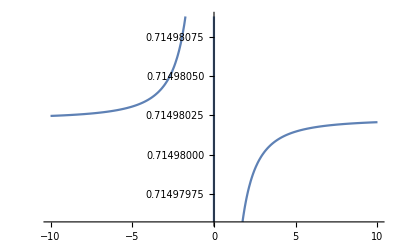

```mathematica
a=0.003
b=0.003
c=0
B0 = 0.5 

F1[x_,y_,z_]=ArcTan[(x+a/2)(y+b/2)/((z+c/2)Sqrt[(x+a/2)^2+(y+b/2)^2+(z+c/2)^2])]

x=0.0005
y=0.0005
B1 = -B0*(F1[-x,y,z+0.0002]+F1[-x,y,-(z+0.0002)]+F1[-x,-y,z+0.0002]+F1[-x,-y,-(z+0.0002)]+F1[x,y,z+0.0002]+F1[x,y,-(z+0.0002)]+F1[x,-y,z]+F1[x,-y,-(+0.0002)])
(*Integrate[B1^2, x,y]*)

Plot[B1,{z,-10, 10}]
```